```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

This file accompanies exercise from Chapter 3: Modeling with Ordinary Differential Equations - D Fey, M Dobrzyński, BN Kholodenko of the book Quantitative Biology: Theory, Computational Methods and Examples of Models

Last modification 27.11.2017

## Modelling two-level cascade without feedbacks with varying total concentrations of components

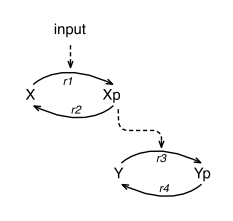

### Definitions of the ODE system

```mathematica
mmfunc[s_,v_,k_]:=v(s/k)/(1+s/k)(* Michaelis-Menten kinetics with Vmax=v, Km=k (halfamx) *)
```

```mathematica
params={
pv1->1,(* Vmax of reaction r1 *)
pv2->.1, (* Vmax of reaction r2 *)
pv3->1, (* Vmax of reaction r3 *)
pv4->.1, (* Vmax of reaction r4 *)
pk1->.5, (* Km of reaction r1 *)
pk2->.1,(* Km of reaction r2 *)
pk3->.5, (* Km of reaction r3 *)
pk4->.1}; (* Km of reaction r4 *)
```

```mathematica
vars={Xp[t],Yp[t]}; (* variables; no need to model X and Y explicitly because X + Xp = Xtot and Y + Yp = Ytot, where Xtot and Ytot are given parameters *)
syst={Xp'[t]==r1-r2,Yp'[t]==r3-r4}; (* ODE equations *)
vsubst={r1->(IN UnitStep[t-INt0]+INbasal)  w1,r2-> w2, r3-> Xp[t] w3, r4-> w4}; (* substitution for reactions 1-4; r1 contains basal stimulation that switches on at time INt0 and assumes level INbasal *)
wsubst={
w1-> mmfunc[X[t],pv1,pk1],w2-> mmfunc[Xp[t],pv2,pk2],
w3-> mmfunc[Y[t],pv3,pk3],w4->mmfunc[Yp[t],pv4,pk4]};
conserv={X[t]->Xtot-Xp[t],Y[t]->Ytot-Yp[t]}; (* conservation of total concentrations of X and Y *)
systsubst=syst/.vsubst/.wsubst/.conserv;
systsubstparams=systsubst/.params;
```

## Plot time course

Interactively explore parameters of the time course:

```mathematica
tMaxPlot = 10;
Manipulate[Plot[
Evaluate[
Yp[t]/.NDSolve[{systsubst/.{
pv1->MANpv1,pv2->MANpv2,pv3->MANpv3,pv4->MANpv4,
pk1->MANpk1,pk2->MANpk2,pk3->MANpk3,pk4->MANpk4,
Xtot->MANXtot,Ytot->MANYtot,
INt0->MANINt0,INbasal->MANINbasal}/.{IN->10^MANIN},Xp[0]==0,Yp[0]==0},{Xp,Yp},{t,0,tMaxPlot}]], 
{t,0,tMaxPlot},
PlotRange->{{0,tMaxPlot}, {0,MANYtot}},
Frame->True,
FrameLabel->{"Time","Yp level"},
BaseStyle->{FontSize->16,FontFamily->"Helvetica",FontWeight->"Bold"},
ImageSize->500], 
{{MANIN, 0}, -2, 2},(* Log10 of input level *)
{{MANINt0, 1}, 0, tMaxPlot},(* time of the stimulus *)
{{MANINbasal, 0.02}, 0, 1}, (* basal level of Y activation *)
{{MANpv1, 10}, 0, 10},
{{MANpv2, 1}, 0, 10},
{{MANpv3, 10}, 0, 10},
{{MANpv4, 1}, 0, 10},
{{MANpk1, .5}, 0, 10},
{{MANpk2, .1}, 0, 10},
{{MANpk3, .5}, 0, 10},
{{MANpk4, .1}, 0, 10},
{{MANXtot, 1}, 0.1, 2},
{{MANYtot, 1}, 0.1, 2}]
```

## Plot dose response at a chosen time point

Interactively explore parameters of the dose response at a time point:

```mathematica
tMaxPlot = 20;
INmin = -3;
INmax = 2;
Manipulate[ListPlot[
Table[{xx,
Evaluate[
Yp[MANt]/.NDSolve[{systsubst/.{
pv1->MANpv1,pv2->MANpv2,
pv3->MANpv3,pv4->MANpv4,
pk1->MANpk1,pk2->MANpk2,
pk3->MANpk3,pk4->MANpk4,
Xtot->MANXtot,Ytot->MANYtot,
INt0->MANINt0,INbasal->MANINbasal}/.{IN->10^xx},Xp[0]==0,Yp[0]==0},{Xp,Yp},{t,0,MANt},
Method->"StiffnessSwitching"][[1]]]}, 
{xx,INmin,INmax,.05}],
Joined->True,
PlotRange->{{-3,2},{0,MANYtot}},
Frame->True,
FrameLabel->{"Log10 input level","Yp level"},
BaseStyle->{FontSize->16,FontFamily->"Helvetica",FontWeight->"Bold"},
ImageSize->500], 
{{MANt, 10}, 0, tMaxPlot}, (* time point at which the dose response is plotted *)
{{MANINt0, 1}, 0, tMaxPlot}, (* time of the stimulus *)
{{MANINbasal, 0.02}, 0, 1}, (* basal level of Y activation *)
{{MANpv1, 10}, 0, 10},
{{MANpv2, 1}, 0, 10},
{{MANpv3, 10}, 0, 10},
{{MANpv4, 1}, 0, 10},
{{MANpk1, .5}, 0, 10},
{{MANpk2, .1}, 0, 10},
{{MANpk3, .5}, 0, 10},
{{MANpk4, .1}, 0, 10},
{{MANXtot, 1}, 0.1, 2},
{{MANYtot, 1}, 0.1, 2}]
```

## Calculate a population of time-dependent functions for a set of inputs

The variability of time-dependent functions is due to variability in the total number of g1, g2, and phosphatases. The variability of g1 and g2 totals is explicitly taken into account in the equations. The variability of total phosphatase concentrations is modeled as variability in Vmax parameters (pv2 and pv4 in equations above) of the Michaelis-Menten reactions. The variability assumes a log-normal distribution

### Parameters of the log-norm distribution

```mathematica
paramLN=FullSimplify[Drop[Solve[{m Exp[(σ^2)/2]==meanLN, Sqrt[(Exp[(σ^2)]-1)*Exp[σ^2] m^2]==stdLN},{m,σ}],1],Assumptions->{meanLN>0,stdLN>0}][[1]]//Quiet
```

{m→meanLN^2/(√(meanLN^2+stdLN^2)),σ→√Log[1+stdLN^2/meanLN^2]}

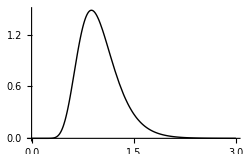

```mathematica
Plot[PDF[LogNormalDistribution[Log[m],σ]/.N[paramLN/.{meanLN->1,stdLN->.3}],x],{x,0,3},
PlotRange->All,
PlotRange->{{0,3},All},
PlotStyle->Black,
BaseStyle->{FontSize->16,FontFamily->"Helvetica"},
ImageSize->250]
```

### Parameters of gamma distribution

Can be used alternatively for varying parameters in ODEs

```mathematica
paramG=FullSimplify[Solve[{k θ==meanG, k^(1/2)θ==stdG},{k,θ}],Assumptions->{meanG>0,stdG>0}][[1]]
```

{k→meanG^2/stdG^2,θ→stdG^2/meanG}

### Parameter substitution

Parameters that follow the log-normal distribution (Xtot, Ytot, pv2, pv4) are omitted in the substitution.

```mathematica
params2={
pv1->10,
pv3->10,
pk1->1,
pk2->.1,
pk3->.1,
pk4->.1};
```

```mathematica
systsubstparams2=systsubst/.params2/.{INt0->10,INbasal->0.02};
```

### Population of N models with random X & Y totals, and Vmax levels

Draw Nrand random numbers for total concentrations of X & Y, and for pv2 & pv4. Mean and STD of the distribution are 1 and 0.3, respectively, for all prameters.

```mathematica
NrandEval=1000;
Xrand=RandomVariate[LogNormalDistribution[Log[m],σ]/.N[paramLN/.{meanLN->1,stdLN->.3}],NrandEval];
Yrand=RandomVariate[LogNormalDistribution[Log[m],σ]/.N[paramLN/.{meanLN->1,stdLN->.3}],NrandEval];
pv2rand=RandomVariate[LogNormalDistribution[Log[m],σ]/.N[paramLN/.{meanLN->1,stdLN->.3}],NrandEval];
pv4rand=RandomVariate[LogNormalDistribution[Log[m],σ]/.N[paramLN/.{meanLN->1,stdLN->.3}],NrandEval];
```

Define range of input values for which the dose response will be calculated:

```mathematica
tabInputEval=Table[10^xx,{xx,-2,0,0.2}]
tabInputEvalLog = Log10[tabInputEval];
```

{0.01,0.0158489,0.0251189,0.0398107,0.0630957,0.1,0.158489,0.251189,0.398107,0.630957,1.}

Define time-points, for which the solution will be plotted:

```mathematica
tabTpointsEval = {.5,1,2,4,8,10,20};
```

Create a table of N numerical time-dependent solutions of the ODE system for a range of input values, on time interval t = [0, tMax] and initial conditions Xp=Yp=0 (total concentration of X and Y is in phosphorylated form):

```mathematica
tMaxEval = Max[tabTpointsEval];
tabFOutOfT=ParallelTable[
NDSolve[{
systsubstparams2/.{
Xtot->Xrand[[ii]],
Ytot->Yrand[[ii]],
pv2->pv2rand[[ii]],
pv4->pv4rand[[ii]],
IN->tabInputEval[[kk]]
},
{Xp[0]==0, Yp[0]==0}},{Xp,Yp},{t,0,tMaxEval},
Method->"StiffnessSwitching"][[1]],
{ii,1,NrandEval},
{kk,1,Length[tabInputEval]}
];//AbsoluteTiming
```

{29.14272,Null}

### Log10 histogram plot for all input values at a chosen time point tPt

```mathematica
tPt = 15; (* make sure that this time point does not exceed tMaxEval above *)
tab1=Table[Yp[t]/.t->tPt/.tabFOutOfT[[All,xx]],{xx,1,Length[tabInputEval]}];
histRes=Table[HistogramList[tab1[[ii]][[All]],40,"PDF"],{ii,1,Length[tabInputEval]}];
histResT=Table[Transpose[{Drop[histRes[[ii]][[1]],-1],histRes[[ii]][[2]]}],{ii,1,Dimensions[histRes][[1]]}];
```

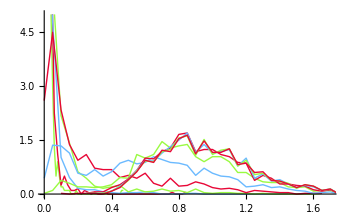

```mathematica
ListPlot[
histResT,
Joined->True,
PlotRange->{{0,1.7},{0,5.0}},
PlotStyle->{{CMYKColor[0.39,.01,.74,0.01]},{CMYKColor[0.02,.97,.77,0.07]},{CMYKColor[0.58,.27,.0,0.0]}},
BaseStyle->{FontSize->16,FontFamily->"Helvetica"},
ImageSize->350]
```

### Median and mean dose response at a time point with (Q1, Q3) boundaries

The dose response is evaluated at time point tPt at input values defined in tabInput

```mathematica
tPt = 15;(* make sure that this time point does not exceed tMaxEval above *)
tabResp=Table[Yp[t]/.t->tPt/.tabFOutOfT[[All,xx]],{xx,1,Length[tabInputEval]}];
```

```mathematica
tabRespMean=Transpose[{tabInputEval,Mean[Transpose[tabResp]]}];
tabRespMedian=Transpose[{tabInputEval,Median[Transpose[tabResp]]}];
tabRespSTDup=Transpose[{tabInputEval,Quantile[Transpose[tabResp],3/4]}]; (* boundary of Q3 quartile *)
tabRespSTDdown=Transpose[{tabInputEval,Quantile[Transpose[tabResp],1/4]}]; (* boundary of Q1 quartile *)
```

Median dose response - solid line,
Mean dose response - dashed black line,
Qartiles - red dashed line

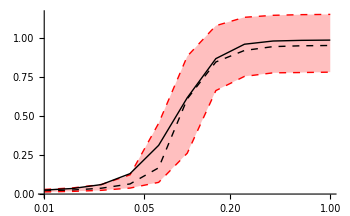

```mathematica
ListLogLinearPlot[{tabRespMedian,tabRespSTDup,tabRespSTDdown, tabRespMean},
Joined->True,
Filling->{2->{1},3->{1}},
FillingStyle->Directive[Opacity[0.25],Red],
PlotStyle->{{Thick,Black,Dashed},{Thick,Red,Dashed},{Thick,Red,Dashed},{Thick,Black}},
BaseStyle->{FontSize->16,FontFamily->"Helvetica"},
ImageSize->350
]
```

### Mean dose response with sample N single-cell dose responses at a time point

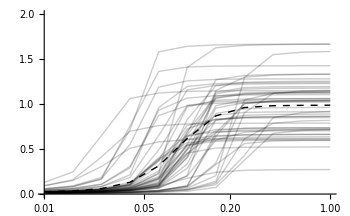

```mathematica
doseN = 50; (* this number has to be smaller than Nrand defined above *)
Show[
ListLogLinearPlot[Table[Transpose[{tabInputEval,tabResp[[All,ii]]}],{ii,1,doseN}],
Joined->True,
PlotRange->{All,{0,2}},
PlotStyle->Opacity[0.2,Black],
BaseStyle->{FontSize->16,FontFamily->"Helvetica"},
ImageSize->350],
ListLogLinearPlot[ tabRespMean,
Joined->True,
PlotStyle->{Thick,Black,Dashed}
]]
```

### Mean time course with sample N time courses for a stimulus level

A table with ODEs was evaluated above for these stimuli:

```mathematica
tabInputEval
```

{0.01,0.0158489,0.0251189,0.0398107,0.0630957,0.1,0.158489,0.251189,0.398107,0.630957,1.}

Index of a value in tabInputEval used to plot time courses:

```mathematica
idxInput = 6;
tabInputEval[[idxInput]]
```

0.1

Create a table with time series on [t0, tMaxEval] range evaluated at an input level given by tabInputEval[[idxInput]] :

```mathematica
t0 = 10;
tabTC=
Transpose[
Table[
Table[{tt-t0,Yp[t]/.tabFOutOfT[[ii,idxInput]]},
{ii,1,NrandEval}]/.t->tt,
{tt,t0,tMaxEval,.1}]];
tabTCmean=Mean[tabTC];
```

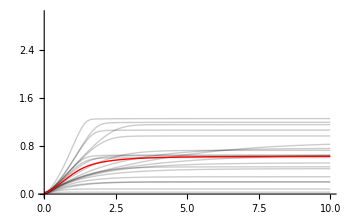

```mathematica
nTracks = 20; (* number of sample time series to plot *)
Show[
ListPlot[
Take[tabTC,nTracks],
Joined->True,
PlotRange->{All,{0,3}},
PlotStyle->{Opacity[0.2,Black]},
BaseStyle->{FontSize->16,FontFamily->"Helvetica"},
ImageSize->350],
ListPlot[tabTCmean,
Joined->True,
PlotRange->{All,{0,3}},
PlotStyle->Red,
BaseStyle->{FontSize->16,FontFamily->"Helvetica"},
ImageSize->350]
]
```

### Log hist plot for given input values at a fixed time point tPt

```mathematica
Nrand=1000; (* this calculation might take a while for large Nrand values *)
Xrand=RandomVariate[LogNormalDistribution[Log[m],σ]/.N[paramLN/.{meanLN->1,stdLN->.3}],Nrand];
Yrand=RandomVariate[LogNormalDistribution[Log[m],σ]/.N[paramLN/.{meanLN->1,stdLN->.3}],Nrand];
pv2rand=RandomVariate[LogNormalDistribution[Log[m],σ]/.N[paramLN/.{meanLN->1,stdLN->.3}],Nrand];
pv4rand=RandomVariate[LogNormalDistribution[Log[m],σ]/.N[paramLN/.{meanLN->1,stdLN->.3}],Nrand];

tabInput={0.01,0.1,1}; (* here just 3 input values used for further plotting *)
tPt = 15; (* time point to evaluate histograms *)
tab1=ParallelTable[
Yp[t]/.t->tPt/.NDSolve[{
systsubstparams2/.{
Xtot->Xrand[[ii]],
Ytot->Yrand[[ii]],
pv2->pv2rand[[ii]],
pv4->pv4rand[[ii]],
IN->tabInput[[kk]]
},
{Xp[0]==0, Yp[0]==0}},{Xp,Yp},{t,0,tPt},
Method->"StiffnessSwitching"][[1]],
{ii,1,Nrand},
{kk,1,Length[tabInput]}
];//Quiet//AbsoluteTiming
```

{7.2682,Null}

```mathematica
histRes=Table[HistogramList[tab1[[All,ii]],80,"PDF"],{ii,1,Length[tabInput]}];
histResT=Table[Transpose[{Drop[histRes[[ii]][[1]],-1],histRes[[ii]][[2]]}],{ii,1,Dimensions[histRes][[1]]}];
```

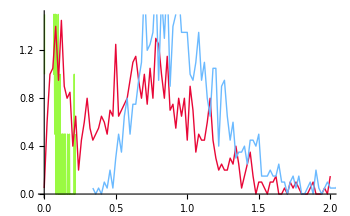

```mathematica
ListPlot[
histResT,
Joined->True,
PlotRange->{{0,2},{0,1.5}},
PlotStyle->{{CMYKColor[0.39,.01,.74,0.01]},{CMYKColor[0.02,.97,.77,0.07]},{CMYKColor[0.58,.27,.0,0.0]}},
BaseStyle->{FontSize->16,FontFamily->"Helvetica"},
ImageSize->350]
```

Black and white version of the plot:

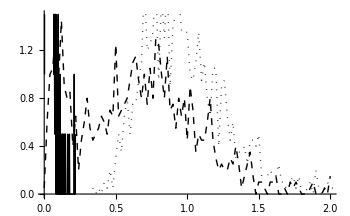

```mathematica
ListPlot[
histResT,
Joined->True,
PlotRange->{{0,2},{0,1.5}},
PlotStyle->{{Thick,Black},{Black,Dashed,Thick},{Black,Dotted,Thick}},
BaseStyle->{FontSize->16,FontFamily->"Helvetica"},
ImageSize->350]
```